```mathematica
SetDirectory["/Users/Apple/Desktop/MidExp"];
```

```mathematica
FileNames["*.xls"]
```

{基准组 5 10 10.xls,FormicAcid100.xls,FormicAcid125.xls,FormicAcid25.xls,FormicAcid75.xls,HCl10.xls,HCl4.xls,HCl6.xls,HCl8.xls,KBr15.xls,KBr20.xls,KBr5.xls,KBr75.xls,TEM30.xls,TEM35.xls,TEM40.xls,TEM45.xls}

```mathematica
FileNames["*.txt"]
```

{10_4HCL.txt,10_HCL-5.txt,10_HCL-6.txt,10_HCL-8.txt,10_KBR-10.txt,10_KBR-15.txt,10_KBR-20.txt,10_KBR-5.txt,10_KBR-6.txt,11_FAcid10.txt,11_FAcid25.txt,11_FAcid35.txt,11_FAcid5.txt,11_FAcid75.txt,11_Temp30.txt,11_Temp35.txt,11_Temp40.txt,11_Temp45.txt,HCL-10.txt}

```mathematica
temprawlist=FileNames["*.xls"][[{1,-4,-3,-2,-1}]];
hclrawlist=FileNames["*.xls"][[{7,1,8,9,6}]];
kbrrawlist=FileNames["*.xls"][[{12,13,1,10,11}]];
farawlist=FileNames["*.xls"][[{4,1,5,2,3}]];
```

```mathematica
thermalrangeselectedlist=MapThread[Take][{First/@Import[#,"Table"]&/@FileNames["*.txt"],RangeSelect}];
```

```mathematica
Import[#,"Table"]&/@FileNames["*.txt"]
```

{{{0.6,1},{0.6,2},{0.7,3},{0.7,4},{0.8,5},{0.7,6},{0.8,7},303,{18.1,311},{18.2,312},{18.2,313},{18.3,314},{18.3,315},{18.4,316},{18.4,317}},17,{1}}
 |  |  |  |

```mathematica
thermalhclrawlist=FileNames["*.txt"][[{1,2,3,-1}]];
thermalkbrrawlist=FileNames["*.txt"][[{8,9,5,6,7}]];
thermalfarawlist=FileNames["*.txt"][[{11,12,13,14,10}]];
thermaltemprawlist=FileNames["*.txt"][[{-7,-5,-4,-3,-2}]];
```

```mathematica
RangeSelector[data_]:=Manipulate[ListLinePlot[data[[i;;j]]],{i,1,j,1},{j,1,Length[data],1}];
```

```mathematica
RangeSelect={{25,317},{38,360},{57,311},{147,311},{30,262},{18,296},{37,425},{16,274},{33,388},{504,725},{692,1863},{266,551},{404,667},{455,767},{156,466},{261,474},{233,398},{69,195},{17,309}};
```

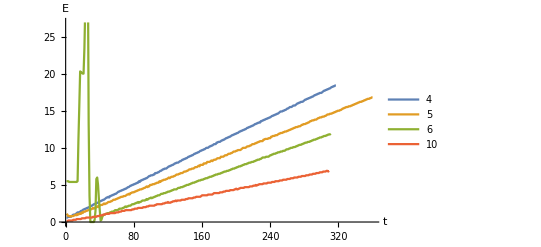

```mathematica
ListLinePlot[First/@Import[#,"Table"]&/@thermalhclrawlist,PlotLegends->{"4","5","6","10"},AxesLabel->{"t","E"}]
```

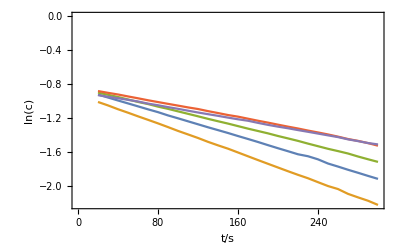

```mathematica
ListLinePlot[Map[{#[[1]],Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@hclrawlist,{2}],Frame->True,Axes->False,FrameLabel->{"t/s","ln(c)"}]
```

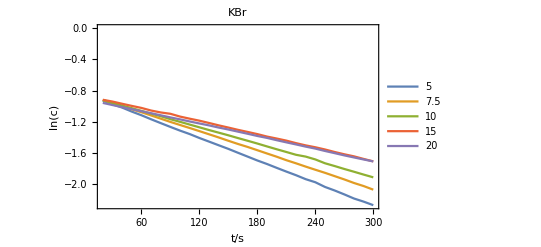

```mathematica
ListLinePlot[Map[{#[[1]],Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@kbrrawlist,{2}],Frame->True,Axes->False,FrameLabel->{"t/s","ln(c)"},PlotRange->All,PlotLabel->"KBr",PlotLegends->{"5","7.5","10","15","20"}]
```

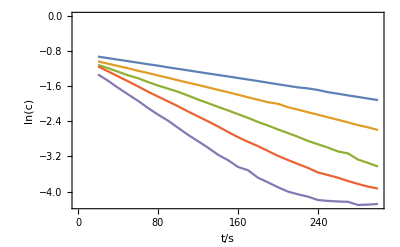

```mathematica
ListLinePlot[Map[{#[[1]],Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@temprawlist,{2}],Frame->True,Axes->False,FrameLabel->{"t/s","ln(c)"}]
```

```mathematica
templist=Map[{#[[1]],Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@temprawlist,{2}];
hcllist=Map[{#[[1]],Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@hclrawlist,{2}];
kbrlist=Map[{#[[1]],Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@kbrrawlist,{2}];
falist=Map[{#[[1]],Log[#[[2]]]}&[Drop[Drop[#,-4],1]]&,Drop[First@Import[#],15]&/@farawlist,{2}];
```

```mathematica
thermaltemplist=First/@Import[#,"Table"]&/@thermaltemprawlist;
```

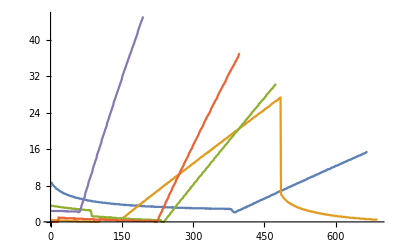

```mathematica
ListLinePlot[thermaltemplist,PlotRange->All]
```

```mathematica
thermaldatapick[list_]:=Module[
```

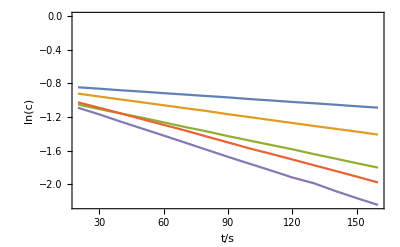

```mathematica
ListLinePlot[Take[#,15]&/@falist,Frame->True,Axes->False,FrameLabel->{"t/s","ln(c)"},PlotRange->All]
```

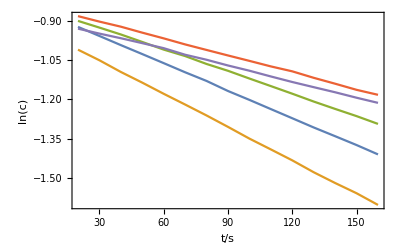

```mathematica
ListLinePlot[Take[#,15]&/@hcllist,Frame->True,Axes->False,FrameLabel->{"t/s","ln(c)"},PlotRange->All]
```

```mathematica
templinelist=LinearModelFit[#,{1,x},x]&/@(Take[#,15]&/@templist);
hcllinelist=LinearModelFit[#,{1,x},x]&/@(Take[#,15]&/@hcllist);
kbrlinelist=LinearModelFit[#,{1,x},x]&/@(Take[#,15]&/@hcllist);
falinelist=LinearModelFit[#,{1,x},x]&/@(Take[#,15]&/@falist);
```

```mathematica
#["RSquared"]&/@templinelist
```

{0.999963,0.999928,0.999431,0.999916,0.999844}

```mathematica
#["RSquared"]&/@hcllinelist
```

{0.999963,0.999948,0.999774,0.99979,0.999584}

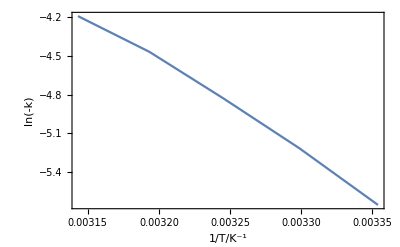

```mathematica
ListLinePlot[Transpose[{1/({25,30,35,40,45}+273.15),Log[-Last/@(#["BestFitParameters"]&/@templinelist)]}],Frame->True,Axes->False,FrameLabel->{"1/T/K^-1","ln(-k)"}]
```

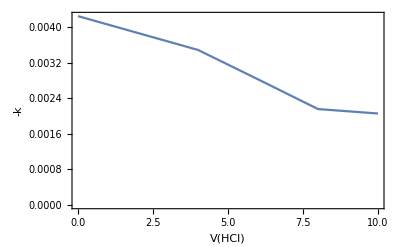

```mathematica
ListLinePlot[Transpose[{{0,4,6,8,10},-Last/@(#["BestFitParameters"]&/@hcllinelist)}],Frame->True,Axes->False,FrameLabel->{"V(HCl)","-k"}]
```

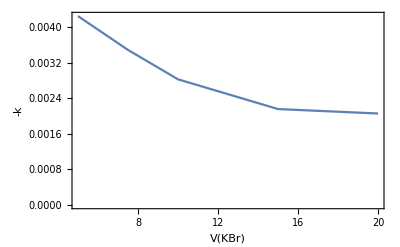

```mathematica
ListLinePlot[Transpose[{{5,7.5,10,15,20},-Last/@(#["BestFitParameters"]&/@kbrlinelist)}],Frame->True,Axes->False,FrameLabel->{"V(KBr)","-k"}]
```

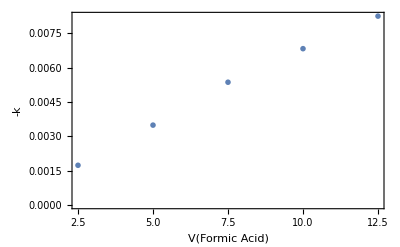

```mathematica
ListPlot[Transpose[{{2.5,5,7.5,10,12.5},-Last/@(#["BestFitParameters"]&/@falinelist)}],Frame->True,Axes->False,FrameLabel->{"V(Formic Acid)","-k"},PlotStyle->PointSize[0.01]]
```

```mathematica
LinearModelFit[Transpose[{{0,4,6,8,10},Log[-Last/@(#["BestFitParameters"]&/@hcllinelist)]}],{1,a},a]["RSquared"]
```

0.996029

```mathematica
FindFit[Transpose[{{2.5,5,7.5,10,12.5},-Last/@(#["BestFitParameters"]&/@kbrlinelist)}],a/(b x +1),{a,b},x]
```

{a→0.00599335,b→0.156229}

```mathematica
NonlinearModelFit[Transpose[{{2.5,5,7.5,10,12.5},-Last/@(#["BestFitParameters"]&/@kbrlinelist)}],a/(b x +1),{a,b},x]["RSquared"]
```

0.998787